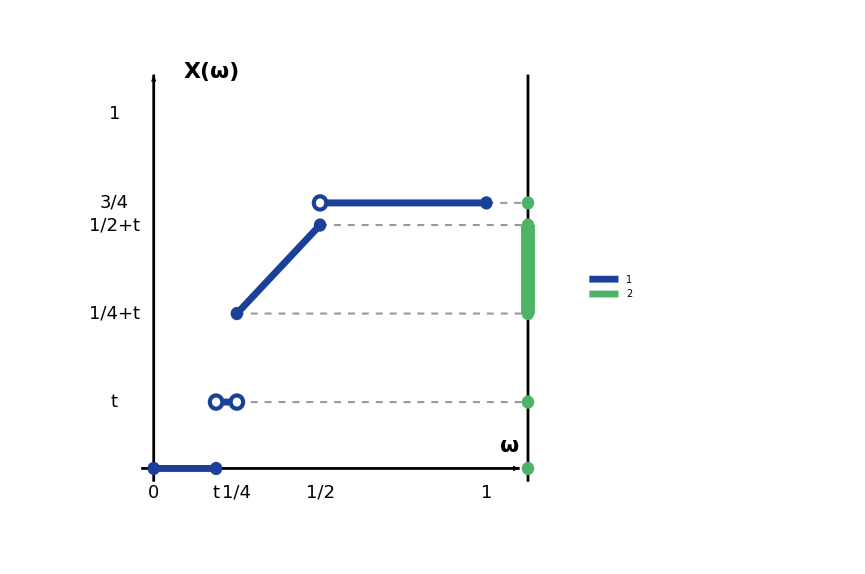

```mathematica
ClearAll[colX, colIm, r, xC, cerrado, abierto, ejes, trozos, guias, ejeCod, etiquetas, grafico1,
  diagrama1];

colX = RGBColor[0.1, 0.25, 0.6];     (* gráfica de X *)
colIm = RGBColor[0.3, 0.7, 0.4];     (* imagen de X *)
r = 0.3;
xC = 18;                             (* eje del codominio, a la derecha *)

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

(* escala del dibujo (t = 3/16): 16 unidades por unidad real, en los dos ejes *)
ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {17.6, 0}}], Arrow[{{0, -0.6}, {0, 17.8}}]};

(* X = 0 en [0,t];  X = t en (t,1/4);  X = ω+t en [1/4,1/2];  X = 3/4 en (1/2,1] *)
trozos = {colX, AbsoluteThickness[5],
   Line[{{0, 0}, {3, 0}}], Line[{{3, 3}, {4, 3}}],
   Line[{{4, 7}, {8, 11}}], Line[{{8, 12}, {16, 12}}],
   cerrado[{0, 0}, colX], cerrado[{3, 0}, colX],
   abierto[{3, 3}, colX], abierto[{4, 3}, colX],
   cerrado[{4, 7}, colX], cerrado[{8, 11}, colX],
   abierto[{8, 12}, colX], cerrado[{16, 12}, colX]};

guias = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{4, 3}, {xC, 3}}], Line[{{4, 7}, {xC, 7}}], Line[{{8, 11}, {xC, 11}}],
   Line[{{16, 12}, {xC, 12}}]};

(* imagen de X = {0} ∪ {t} ∪ [1/4+t, 1/2+t] ∪ {3/4} *)
ejeCod = {Black, AbsoluteThickness[2], Line[{{xC, -0.6}, {xC, 17.8}}],
   colIm, AbsoluteThickness[10], CapForm["Butt"], Line[{{xC, 7}, {xC, 11}}],
   cerrado[{xC, 0}, colIm], cerrado[{xC, 3}, colIm], cerrado[{xC, 7}, colIm],
   cerrado[{xC, 11}, colIm], cerrado[{xC, 12}, colIm]};

etiquetas = {Black,
   Table[Text[Style[p[[2]], 18], {p[[1]], -1.1}],
    {p, {{0, "0"}, {3, "t"}, {4, "1/4"}, {8, "1/2"}, {16, "1"}}}],
   Table[Text[Style[p[[2]], 18], {-1.9, p[[1]]}],
    {p, {{3, "t"}, {7, "1/4+t"}, {11, "1/2+t"}, {12, "3/4"}, {16, "1"}}}],
   Text[Style["ω", 22, Bold], {17.1, 1.0}],
   Text[Style["X(ω)", 22, Bold], {2.8, 17.9}]};

grafico1 = Graphics[{guias, ejes, trozos, ejeCod, etiquetas},
   PlotRange -> {{-3.8, 19.8}, {-2.4, 18.8}}, ImageSize -> 640];

diagrama1 = Legended[grafico1,
   SwatchLegend[{colX, colIm}, {"gráfica de X", "imagen de X"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama1

Export[CloudObject["T3_P52_a"], diagrama1,"PNG", Background -> None,ImageResolution -> 300];
```

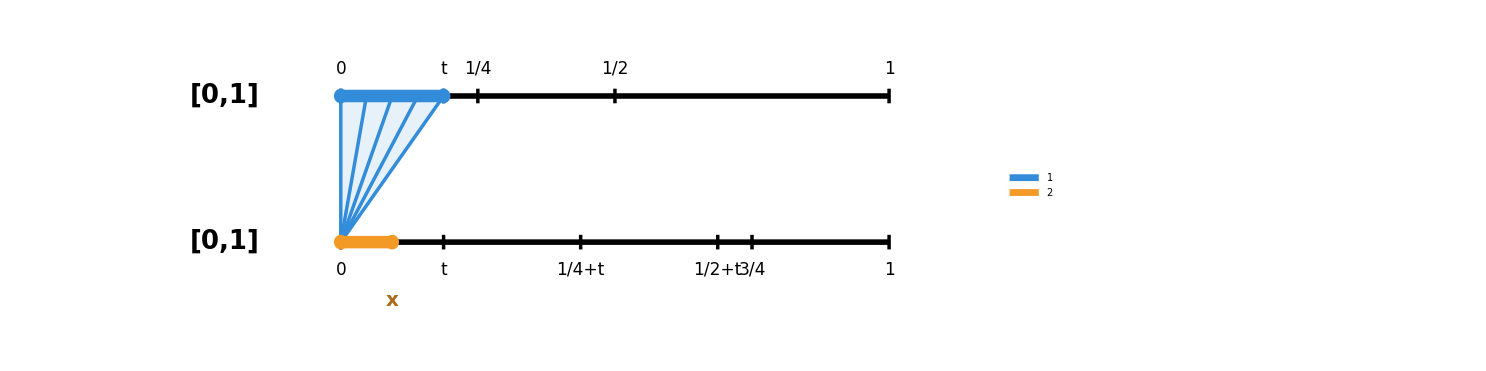
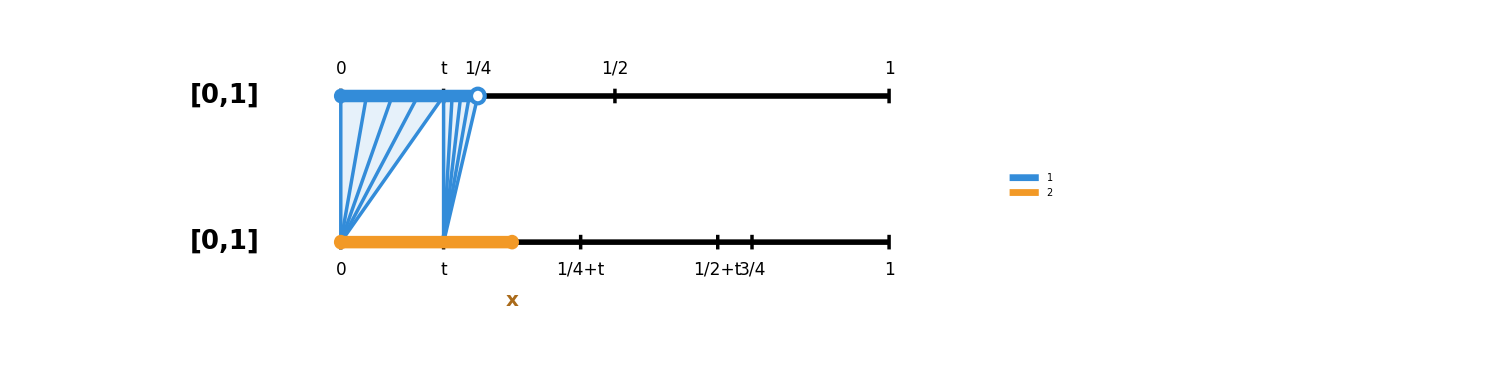
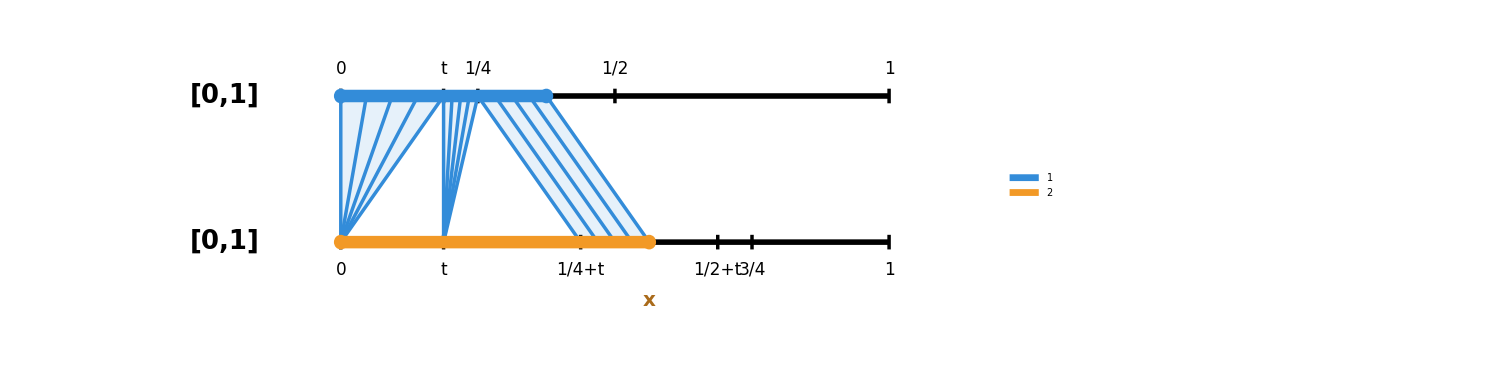
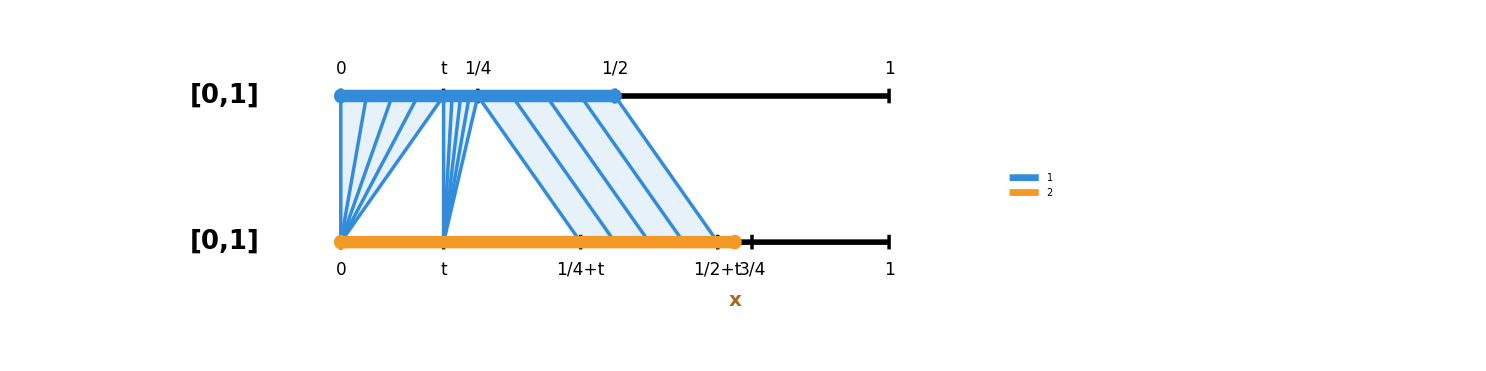
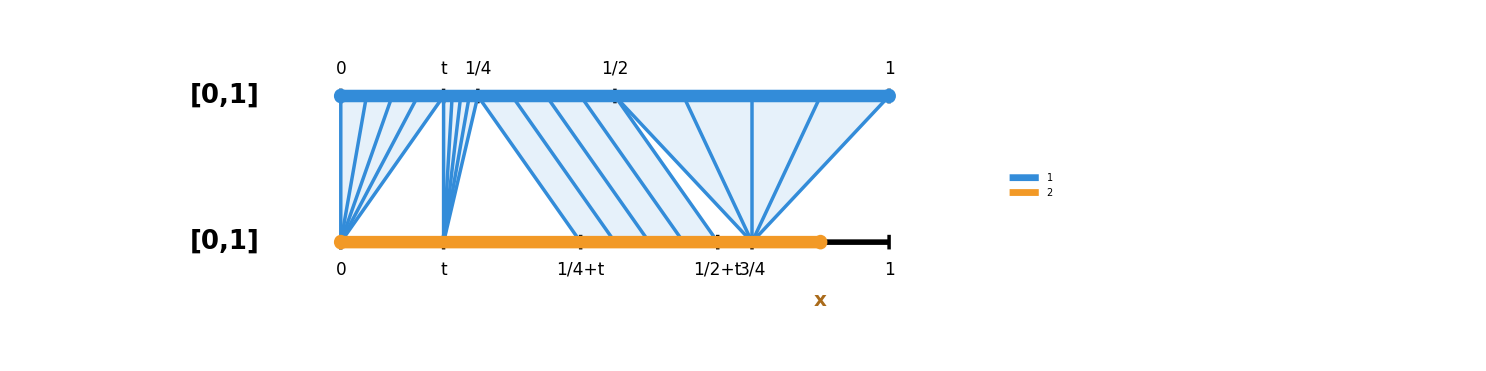

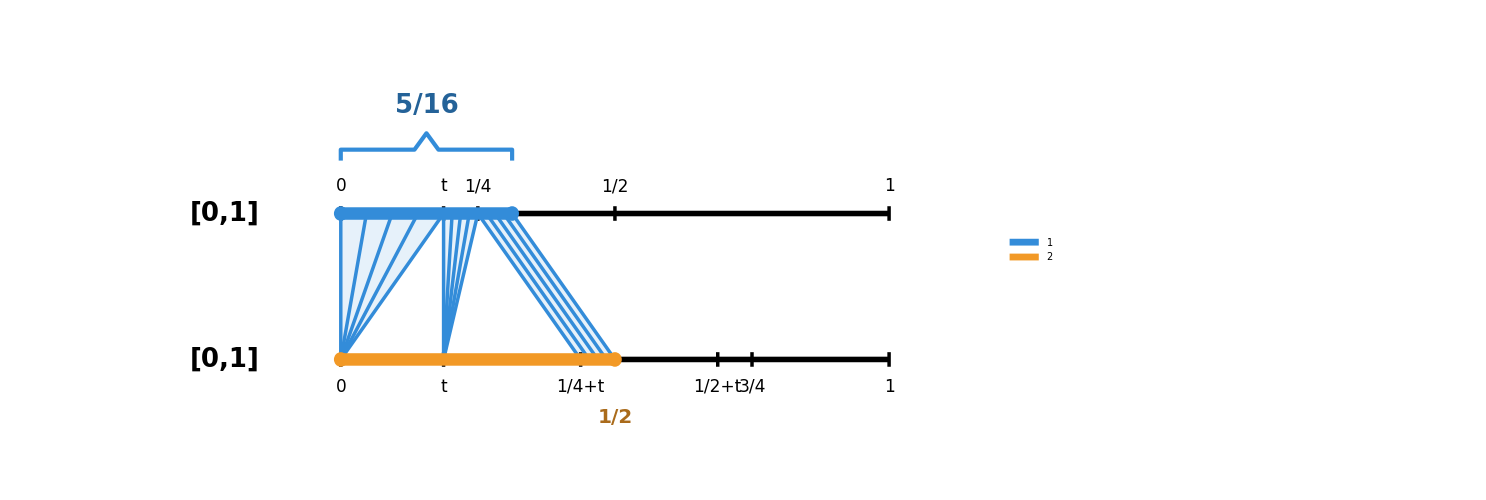
{-Graphics-,-Graphics-}

```mathematica
ClearAll[yTop, yBot, colO, colN, rr, cerrado, abierto, baseArriba, baseAbajo, pieza, segTop,
  intervaloAbajo, llaveArriba, leyendaCon, caso, casosA, casosCD];

yTop = 4; yBot = 0;
colO = RGBColor[0.2, 0.55, 0.85];    (* antiimagen, en el espacio de origen *)
colN = RGBColor[0.95, 0.6, 0.15];    (* intervalo, en el espacio de llegada *)
rr = 0.2;

cerrado[p_, col_] := {col, Disk[p, rr]};
abierto[p_, col_] := {White, Disk[p, rr], col, AbsoluteThickness[3], Circle[p, rr]};

(* [0,1] arriba y [0,1] abajo, a la misma escala: 16 unidades de dibujo por unidad real *)
baseArriba = {
   {Black, AbsoluteThickness[4], Line[{{0, yTop}, {16, yTop}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yTop - 0.2}, {p[[1]], yTop + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yTop + 0.75}]},
    {p, {{0, "0"}, {3, "t"}, {4, "1/4"}, {8, "1/2"}, {16, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.4, yTop}]};

baseAbajo = {
   {Black, AbsoluteThickness[4], Line[{{0, yBot}, {16, yBot}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yBot - 0.2}, {p[[1]], yBot + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yBot - 0.75}]},
    {p, {{0, "0"}, {3, "t"}, {7, "1/4+t"}, {11, "1/2+t"}, {12, "3/4"}, {16, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.4, yBot}]};

(* un tramo de X: el intervalo {t1,t2} de arriba va al intervalo {b1,b2} de abajo.
   Si b1 = b2 es un abanico (tramo constante); si no, son líneas paralelas (tramo afín) *)
pieza[t1_, t2_, b1_, b2_] := {
   {colO, Opacity[0.12], Polygon[{{t1, yTop}, {t2, yTop}, {b2, yBot}, {b1, yBot}}]},
   {colO, AbsoluteThickness[2.5],
    Table[Line[{{t1 + s (t2 - t1), yTop}, {b1 + s (b2 - b1), yBot}}],
     {s, {0, 0.25, 0.5, 0.75, 1}}]}};

(* la antiimagen sobre el origen: {x1, cerrado1, x2, cerrado2} *)
segTop[{x1_, c1_, x2_, c2_}] := {colO, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{x1, yTop}, {x2, yTop}}],
   If[c1, cerrado[{x1, yTop}, colO], abierto[{x1, yTop}, colO]],
   If[c2, cerrado[{x2, yTop}, colO], abierto[{x2, yTop}, colO]]};

(* el intervalo del espacio de llegada, con etiquetas en una fila inferior *)
intervaloAbajo[{a_, ca_, b_, cb_}, etqs_List] := {colN, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{a, yBot}, {b, yBot}}],
   If[ca, cerrado[{a, yBot}, colN], abierto[{a, yBot}, colN]],
   If[cb, cerrado[{b, yBot}, colN], abierto[{b, yBot}, colN]],
   Table[Text[Style[e[[2]], 20, Bold, Darker[colN, 0.3]], {e[[1]], yBot - 1.6}], {e, etqs}]};

(* llave sobre el origen que mide la antiimagen *)
llaveArriba[xa_, xb_, txt_] := Module[{y0 = yTop + 1.45, m = (xa + xb)/2},
   {colO, AbsoluteThickness[3],
    Line[{{xa, y0}, {xa, y0 + 0.3}, {m - 0.35, y0 + 0.3}, {m, y0 + 0.75},
      {m + 0.35, y0 + 0.3}, {xb, y0 + 0.3}, {xb, y0}}],
    Text[Style[txt, 26, Bold, Darker[colO, 0.3]], {m, y0 + 1.5}]}];

leyendaCon[txt_] := SwatchLegend[{colO, colN}, {"antiimagen", txt},
   LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20];

(* arr: intervalo de llegada; pre: antiimagen; piezas: tramos de X que se dibujan;
   etqs: etiquetas bajo el intervalo; llave: {x1, x2, texto} o None *)
caso[arr_, pre_List, piezas_List, etqs_List, llave_, txtLey_] := Legended[
   Graphics[{baseArriba, baseAbajo,
     Table[pieza @@ p, {p, piezas}],
     Table[segTop[p], {p, pre}],
     intervaloAbajo[arr, etqs],
     If[llave === None, {}, llaveArriba @@ llave]},
    PlotRange -> {{-6.2, 18.4},
      {yBot - 2.6, If[llave === None, yTop + 1.7, yTop + 4.6]}},
    ImageSize -> 1100],
   leyendaCon[txtLey]];

(* tramos de X: [0,t] -> 0,  (t,1/4) -> t,  [1/4,1/2] -> [1/4+t,1/2+t],  (1/2,1] -> 3/4 *)
(* apartado a): un caso por rama, con x = 3/32, 5/16, 9/16, 23/32 y 7/8 *)
casosA = {
   caso[{0, True, 1.5, True}, {{0, True, 3, True}},
    {{0, 3, 0, 0}}, {{1.5, "x"}}, None, "intervalo [0,x]"],                      (* 0 <= x < t *)
   caso[{0, True, 5, True}, {{0, True, 4, False}},
    {{0, 3, 0, 0}, {3, 4, 3, 3}}, {{5, "x"}}, None, "intervalo [0,x]"],          (* t <= x < 1/4+t *)
   caso[{0, True, 9, True}, {{0, True, 6, True}},
    {{0, 3, 0, 0}, {3, 4, 3, 3}, {4, 6, 7, 9}}, {{9, "x"}}, None,
    "intervalo [0,x]"],                                                          (* 1/4+t <= x <= 1/2+t *)
   caso[{0, True, 11.5, True}, {{0, True, 8, True}},
    {{0, 3, 0, 0}, {3, 4, 3, 3}, {4, 8, 7, 11}}, {{11.5, "x"}}, None,
    "intervalo [0,x]"],                                                          (* 1/2+t < x < 3/4 *)
   caso[{0, True, 14, True}, {{0, True, 16, True}},
    {{0, 3, 0, 0}, {3, 4, 3, 3}, {4, 8, 7, 11}, {8, 16, 12, 12}}, {{14, "x"}},
    None, "intervalo [0,x]"]};                                                   (* 3/4 <= x <= 1 *)

(* apartados c) y d): los intervalos [0,1/2] y [5/16,1], con la longitud de su antiimagen *)
casosCD = {
   caso[{0, True, 8, True}, {{0, True, 5, True}},
    {{0, 3, 0, 0}, {3, 4, 3, 3}, {4, 5, 7, 8}}, {{8, "1/2"}},
    {0, 5, "5/16"}, "intervalo"],
   caso[{5, True, 16, True}, {{4, True, 16, True}},
    {{4, 8, 7, 11}, {8, 16, 12, 12}}, {{5, "5/16"}},
    {4, 16, "3/4"}, "intervalo"]};

casosA

casosCD

(* se guardan como T3_P52_a1.png ... a5.png y T3_P52_c1.png, c2.png *)
Do[Export[CloudObject["T3_P52_a" <> ToString[k]], casosA[[k]],"PNG", Background -> None,ImageResolution ->300], {k, 1, 5}];
Do[Export[CloudObject["T3_P52_c" <> ToString[k]], casosCD[[k]],"PNG", Background -> None,ImageResolution ->300], {k, 1, 2}];
```

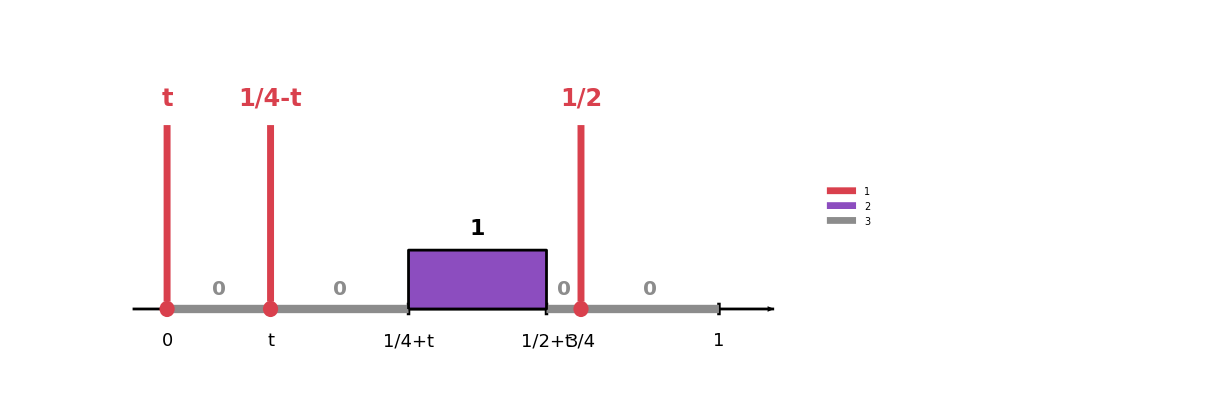

```mathematica
ClearAll[colDens, colAt, colCero, hD, yA, r, ejeBase, dens, ceros, atomos, grafico3, diagrama3];

colDens = RGBColor[0.55, 0.3, 0.75];
colAt = RGBColor[0.85, 0.25, 0.3];
colCero = GrayLevel[0.55];
hD = 1.6;     (* altura que representa densidad 1 *)
yA = 5;       (* altura (solo gráfica) de las flechas de masa puntual *)
r = 0.22;

ejeBase = {Black, AbsoluteThickness[2], Arrowheads[0.025], Arrow[{{-1, 0}, {17.6, 0}}],
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], -0.17}, {p[[1]], 0.17}}],
     Text[Style[p[[2]], 18], {p[[1]], -0.85}]},
    {p, {{0, "0"}, {3, "t"}, {7, "1/4+t"}, {11, "1/2+t"}, {12, "3/4"}, {16, "1"}}}]};

(* densidad 1 en [1/4+t, 1/2+t] *)
dens = {colDens, EdgeForm[{Black, AbsoluteThickness[2]}], Rectangle[{7, 0}, {11, hD}],
   Black, Text[Style["1", 22, Bold], {9, hD + 0.6}]};

(* masa 0 en los huecos *)
ceros = {colCero, AbsoluteThickness[6], CapForm["Butt"],
   Line[{{0, 0}, {3, 0}}], Line[{{3, 0}, {7, 0}}],
   Line[{{11, 0}, {12, 0}}], Line[{{12, 0}, {16, 0}}],
   Text[Style["0", 20, Bold, colCero], {1.5, 0.55}],
   Text[Style["0", 20, Bold, colCero], {5, 0.55}],
   Text[Style["0", 20, Bold, colCero], {11.5, 0.55}],
   Text[Style["0", 20, Bold, colCero], {14, 0.55}]};

(* masas puntuales: t en el 0, 1/4-t en t y 1/2 en 3/4 *)
atomos = Table[{colAt, AbsoluteThickness[5], Arrowheads[0.035],
    Arrow[{{p[[1]], 0.2}, {p[[1]], yA}}], Disk[{p[[1]], 0}, r],
    Text[Style[p[[2]], 24, Bold, colAt], {p[[1]], yA + 0.75}]},
   {p, {{0, "t"}, {3, "1/4-t"}, {12, "1/2"}}}];

grafico3 = Graphics[{ejeBase, dens, ceros, atomos},
   PlotRange -> {{-1.8, 18.2}, {-1.8, 7.4}}, ImageSize -> 900];

diagrama3 = Legended[grafico3,
   SwatchLegend[{colAt, colDens, colCero}, {"masa puntual", "densidad", "masa 0"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama3

Export[CloudObject["T3_P52_PX"], diagrama3,"PNG",Background -> None,ImageResolution -> 300];
```

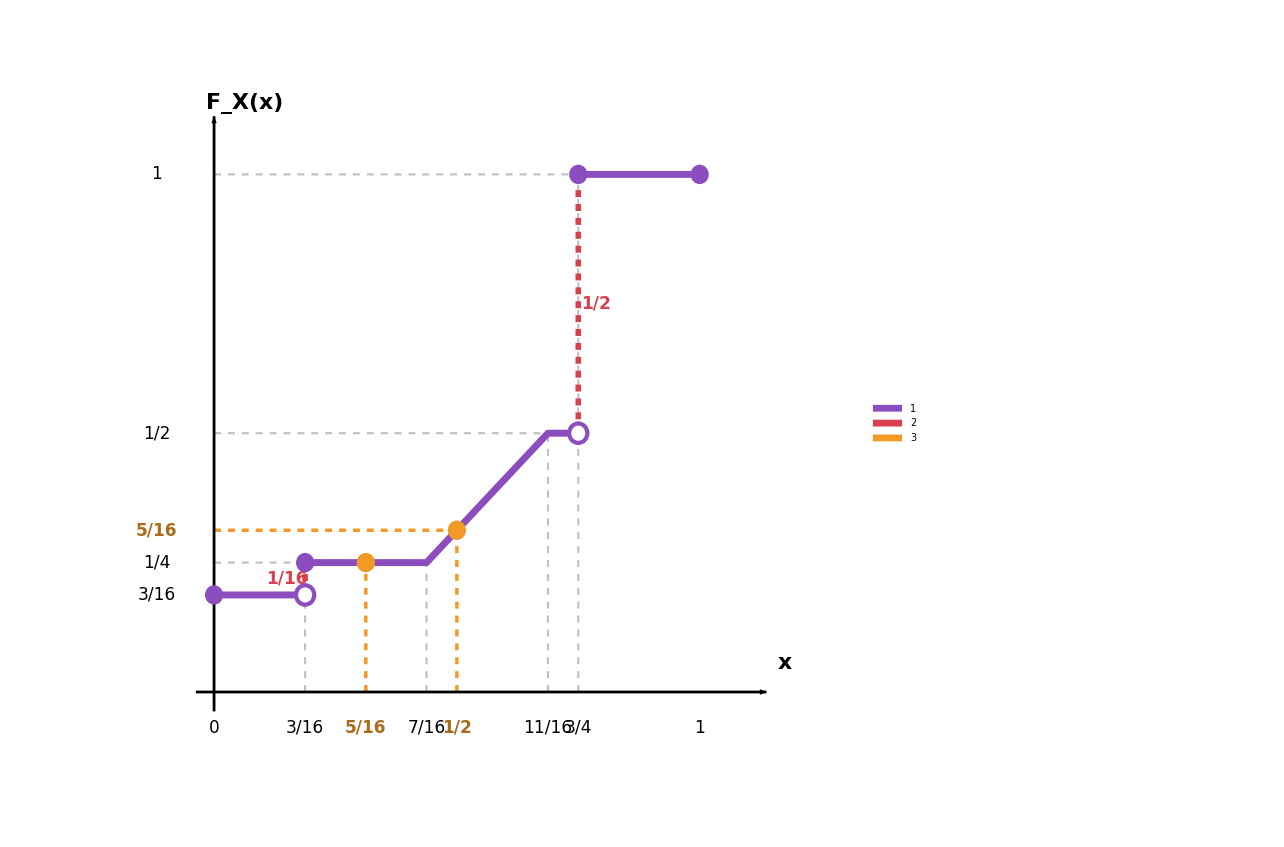

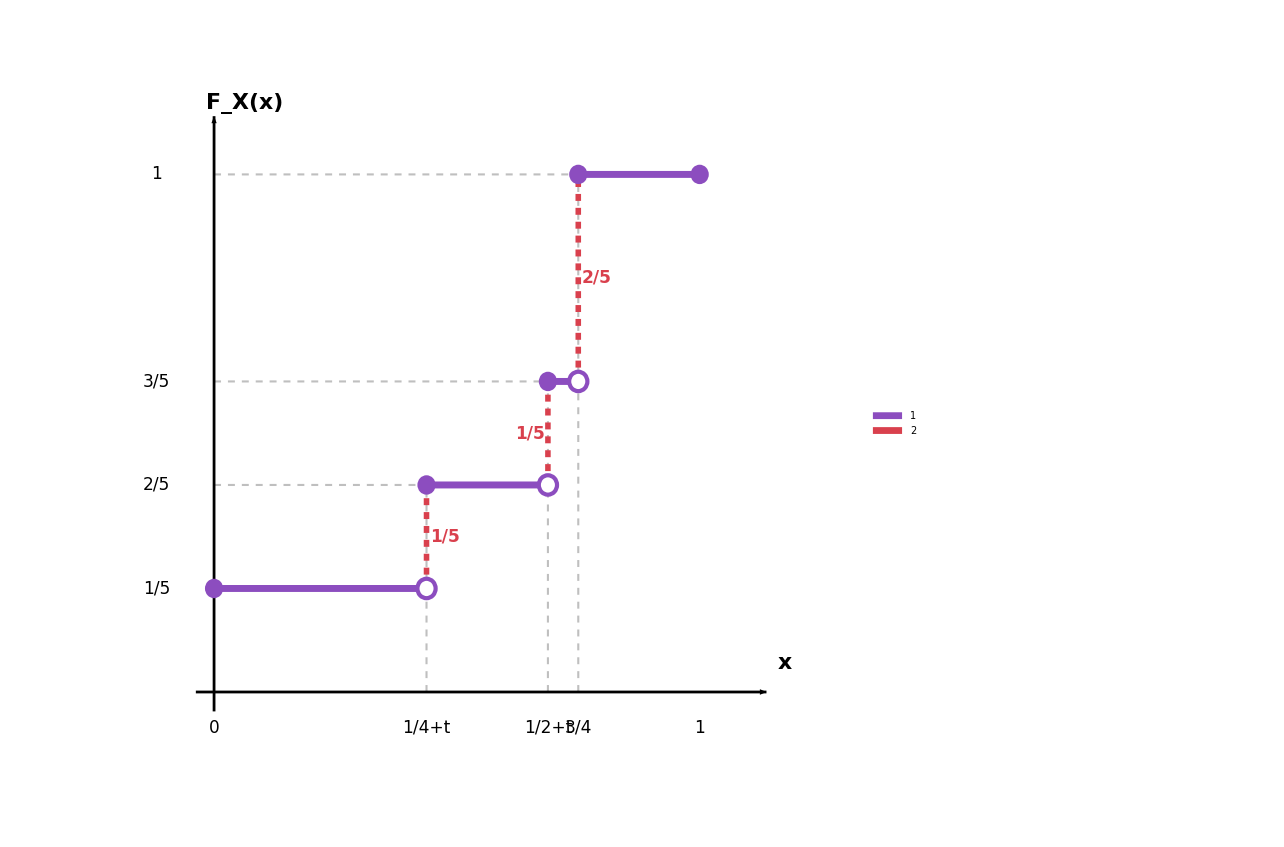

```mathematica
ClearAll[colCDF, colSalto, colPto, r, cerrado, abierto, ejes, guiasL, guiasPto, saltosL, curvaL,
  puntosL, etiquetasL, graficoL, diagramaL, guiasM, saltosM, curvaM, puntosM, etiquetasM,
  graficoM, diagramaM];

colCDF = RGBColor[0.55, 0.3, 0.75];
colSalto = RGBColor[0.85, 0.25, 0.3];
colPto = RGBColor[0.95, 0.6, 0.15];
r = 0.3;

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

(* escala del dibujo: 16 unidades por unidad real, en los dos ejes *)
ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {18.2, 0}}], Arrow[{{0, -0.6}, {0, 17.8}}]};

(* ============ Diagrama A: F_X bajo λ, con t = 3/16 ============ *)
guiasL = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Table[Line[{{p[[1]], 0}, p}], {p, {{3, 4}, {7, 4}, {11, 8}, {12, 16}}}],
   Line[{{0, 4}, {3, 4}}], Line[{{0, 8}, {11, 8}}], Line[{{0, 16}, {12, 16}}]};

(* los valores de c): F(5/16^-) = 1/4 y F(1/2) = 5/16 *)
guiasPto = {colPto, Dashed, AbsoluteThickness[2.5],
   Line[{{5, 0}, {5, 4}}], Line[{{8, 0}, {8, 5}}], Line[{{0, 5}, {8, 5}}]};

(* 3/16 en [0,3/16);  1/4 en [3/16,7/16);  x-3/16 en [7/16,11/16];  1/2 hasta 3/4;  1 desde 3/4 *)
curvaL = {colCDF, AbsoluteThickness[5],
   Line[{{0, 3}, {3, 3}}], Line[{{3, 4}, {7, 4}, {11, 8}, {12, 8}}],
   Line[{{12, 16}, {16, 16}}]};

saltosL = {colSalto, Dashed, AbsoluteThickness[4],
   Line[{{3, 3}, {3, 4}}], Line[{{12, 8}, {12, 16}}]};

puntosL = {cerrado[{0, 3}, colCDF], abierto[{3, 3}, colCDF], cerrado[{3, 4}, colCDF],
   abierto[{12, 8}, colCDF], cerrado[{12, 16}, colCDF], cerrado[{16, 16}, colCDF],
   cerrado[{5, 4}, colPto], cerrado[{8, 5}, colPto]};

etiquetasL = {Black,
   Table[Text[Style[p[[2]], 17], {p[[1]], -1.1}],
    {p, {{0, "0"}, {3, "3/16"}, {7, "7/16"}, {11, "11/16"}, {12, "3/4"}, {16, "1"}}}],
   Table[Text[Style[p[[2]], 17], {-1.9, p[[1]]}],
    {p, {{3, "3/16"}, {4, "1/4"}, {8, "1/2"}, {16, "1"}}}],
   {Darker[colPto, 0.3],
    Text[Style["5/16", 17, Bold], {5, -1.1}],
    Text[Style["1/2", 17, Bold], {8, -1.1}],
    Text[Style["5/16", 17, Bold], {-1.9, 5}]},
   Text[Style["x", 22, Bold], {18.8, 0.9}],
   Text[Style[Row[{Subscript["F", "X"], "(x)"}], 22, Bold], {1.0, 18.2}, {-1, 0}],
   Text[Style["1/16", 17, Bold, colSalto], {2.4, 3.5}, {1, 0}],
   Text[Style["1/2", 17, Bold, colSalto], {12.6, 12}, {-1, 0}]};

graficoL = Graphics[{guiasL, guiasPto, ejes, saltosL, curvaL, puntosL, etiquetasL},
   PlotRange -> {{-3.4, 20.6}, {-2.4, 19.0}}, ImageSize -> 950];

diagramaL = Legended[graficoL,
   SwatchLegend[{colCDF, colSalto, colPto},
    {"función de distribución", "saltos (masas puntuales)", "valores de c)"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagramaL

Export[CloudObject["T3_P52_FX"], diagramaL,"PNG", Background -> None,ImageResolution -> 300];

(* ============ Diagrama B: función de distribución bajo la medida discreta μ ============ *)
guiasM = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Table[Line[{{p[[1]], 0}, p}], {p, {{7, 6.4}, {11, 9.6}, {12, 16}}}],
   Line[{{0, 6.4}, {7, 6.4}}], Line[{{0, 9.6}, {11, 9.6}}], Line[{{0, 16}, {12, 16}}]};

(* 1/5 en [0,1/4+t);  2/5 hasta 1/2+t;  3/5 hasta 3/4;  1 desde 3/4 (valores 3.2, 6.4, 9.6 y 16) *)
curvaM = {colCDF, AbsoluteThickness[5],
   Line[{{0, 3.2}, {7, 3.2}}], Line[{{7, 6.4}, {11, 6.4}}],
   Line[{{11, 9.6}, {12, 9.6}}], Line[{{12, 16}, {16, 16}}]};

saltosM = {colSalto, Dashed, AbsoluteThickness[4],
   Line[{{7, 3.2}, {7, 6.4}}], Line[{{11, 6.4}, {11, 9.6}}], Line[{{12, 9.6}, {12, 16}}]};

puntosM = {cerrado[{0, 3.2}, colCDF], abierto[{7, 3.2}, colCDF], cerrado[{7, 6.4}, colCDF],
   abierto[{11, 6.4}, colCDF], cerrado[{11, 9.6}, colCDF], abierto[{12, 9.6}, colCDF],
   cerrado[{12, 16}, colCDF], cerrado[{16, 16}, colCDF]};

etiquetasM = {Black,
   Table[Text[Style[p[[2]], 17], {p[[1]], -1.1}],
    {p, {{0, "0"}, {7, "1/4+t"}, {11, "1/2+t"}, {12, "3/4"}, {16, "1"}}}],
   Table[Text[Style[p[[2]], 17], {-1.9, p[[1]]}],
    {p, {{3.2, "1/5"}, {6.4, "2/5"}, {9.6, "3/5"}, {16, "1"}}}],
   Text[Style["x", 22, Bold], {18.8, 0.9}],
   Text[Style[Row[{Subscript["F", "X"], "(x)"}], 22, Bold], {1.0, 18.2}, {-1, 0}],
   Text[Style["1/5", 17, Bold, colSalto], {7.6, 4.8}, {-1, 0}],
   Text[Style["1/5", 17, Bold, colSalto], {10.4, 8.0}, {1, 0}],
   Text[Style["2/5", 17, Bold, colSalto], {12.6, 12.8}, {-1, 0}]};

graficoM = Graphics[{guiasM, ejes, saltosM, curvaM, puntosM, etiquetasM},
   PlotRange -> {{-3.4, 20.6}, {-2.4, 19.0}}, ImageSize -> 950];

diagramaM = Legended[graficoM,
   SwatchLegend[{colCDF, colSalto}, {"función de distribución", "saltos = masas puntuales"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagramaM

Export[CloudObject["T3_P52_e_F"], diagramaM,"PNG",Background -> None,ImageResolution ->300];
```

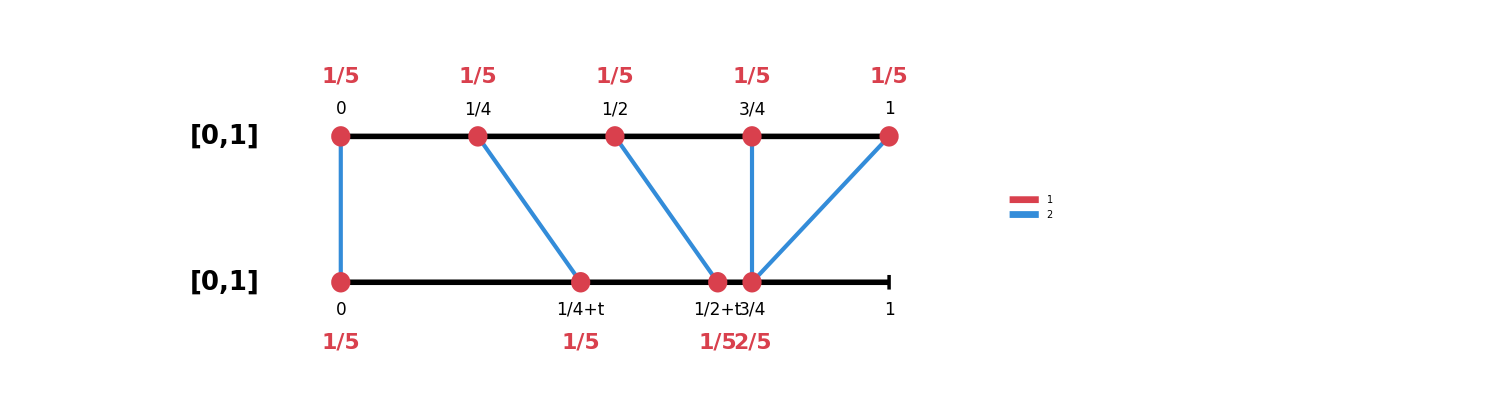

```mathematica
ClearAll[yTop, yBot, colO, colAt, rr, cerrado, origen, destino, baseArriba, baseAbajo, lineas,
  masasArriba, masasAbajo, grafico5, diagrama5];

yTop = 4; yBot = 0;
colO = RGBColor[0.2, 0.55, 0.85];    (* la aplicación X *)
colAt = RGBColor[0.85, 0.25, 0.3];   (* masas puntuales *)
rr = 0.28;

cerrado[p_, col_] := {col, Disk[p, rr]};

(* D = {0, 1/4, 1/2, 3/4, 1}  y  X(D) = {0, 1/4+t, 1/2+t, 3/4, 3/4}, con t = 3/16 *)
origen = {0, 4, 8, 12, 16};
destino = {0, 7, 11, 12, 12};

baseArriba = {
   {Black, AbsoluteThickness[4], Line[{{0, yTop}, {16, yTop}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yTop - 0.2}, {p[[1]], yTop + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yTop + 0.75}]},
    {p, {{0, "0"}, {4, "1/4"}, {8, "1/2"}, {12, "3/4"}, {16, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.4, yTop}]};

baseAbajo = {
   {Black, AbsoluteThickness[4], Line[{{0, yBot}, {16, yBot}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yBot - 0.2}, {p[[1]], yBot + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yBot - 0.75}]},
    {p, {{0, "0"}, {7, "1/4+t"}, {11, "1/2+t"}, {12, "3/4"}, {16, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.4, yBot}]};

(* una línea por cada átomo: de su posición arriba a su imagen abajo *)
lineas = {colO, AbsoluteThickness[3],
   Table[Line[{{origen[[i]], yTop}, {destino[[i]], yBot}}], {i, 1, 5}]};

(* arriba, μ = 1/5 en cada punto de D *)
masasArriba = Table[{colAt, Disk[{origen[[i]], yTop}, rr],
    Text[Style["1/5", 22, Bold, colAt], {origen[[i]], yTop + 1.65}]}, {i, 1, 5}];

(* abajo, la masa inducida: 3/4 recibe dos líneas *)
masasAbajo = Table[{colAt, Disk[{p[[1]], yBot}, rr],
    Text[Style[p[[2]], 22, Bold, colAt], {p[[1]], yBot - 1.65}]},
   {p, {{0, "1/5"}, {7, "1/5"}, {11, "1/5"}, {12, "2/5"}}}];

grafico5 = Graphics[{baseArriba, baseAbajo, lineas, masasArriba, masasAbajo},
   PlotRange -> {{-6.2, 18.4}, {yBot - 2.6, yTop + 2.7}}, ImageSize -> 1100];

diagrama5 = Legended[grafico5,
   SwatchLegend[{colAt, colO}, {"masa puntual", "aplicación X"},
    LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20]];

diagrama5

Export[CloudObject["T3_P52_b"], diagrama5,"PNG", Background -> None,ImageResolution -> 300];
```